```mathematica
Predicting Gold Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- PAXG hourly price: Recent (≥ 2020) data - Gemini.

## In This Notebook

LPPLS model implementation (2026 ed.) for Gold price in USD.
Uses PAXG price as a proxy for Gold’s price, due to current lack of access to high quality (hourly) Spot Gold price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPriceDate="2020-11-01"
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2020-11-01

2025-12-29

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Gemini_PAXGUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

{2025-12-29,23:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={#[[1]]/1000, #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

45260

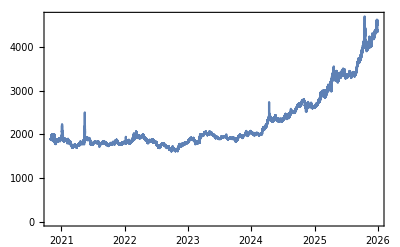

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Gold(PAXG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Gold(PAXG)_price-hourly-20201101-20251229.csv

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Sat 31 Oct 2020 05:00:00GMT+1,Tue 30 Dec 2025 00:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-01-01", lastPriceDate}, {"2025-01-01", lastPriceDate}}
```

{{2024-01-01,2025-12-29},{2025-01-01,2025-12-29}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1704063600,1766962800},{1735686000,1766962800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{728,362}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1704063600,7.61955},{1735686000,7.87335}}

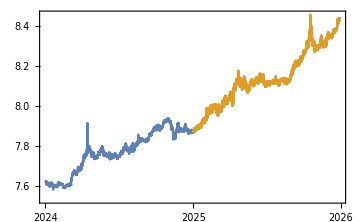

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.11145,0.974255},{1.2526,0.9616}}

```mathematica
Length/@bubblesScaled
```

{17473,8689}

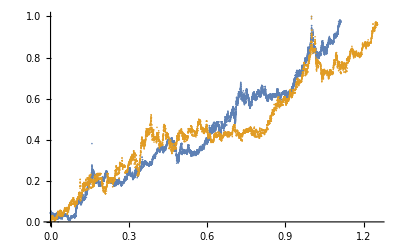

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Gold(PAXG)"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold(PAXG)1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold(PAXG)2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.1
```

0.1

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{15.7054,17452.3},{15.7132,8668.29}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{6.71485,0.0196157,0.000561609},{5.1582,0.0243952,0.00098632}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

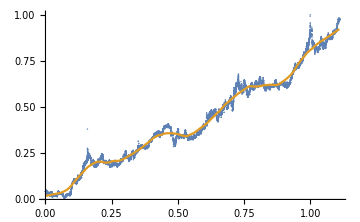
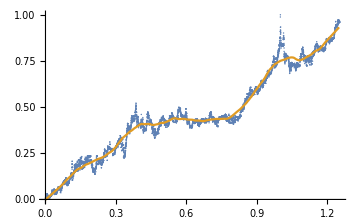

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

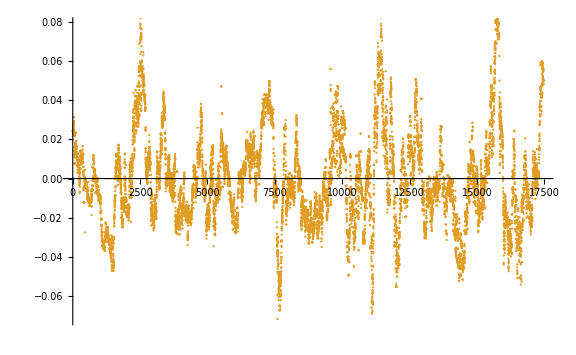
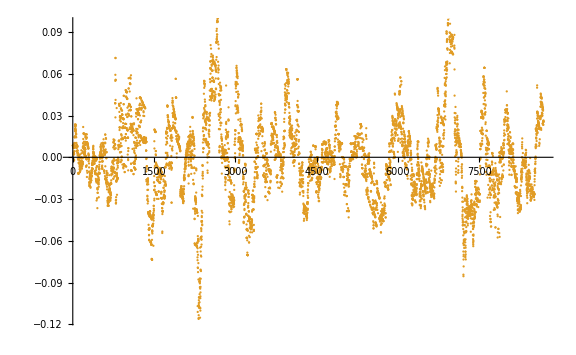

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.02402,0.0298951}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{10.0824,7.76477}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{10.0824 > 6.71485,7.76477 > 5.1582}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0240323,0.0299207}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0240323 > 0.0196157,0.0299207 > 0.0243952}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0196124,0.0243869}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0240357,0.0299294}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0240357 > 0.0196157,0.0299294 > 0.0243952}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0196152,0.024394}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{15.7132,8668.29}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.2526

2.41834

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.019337

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0276243

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{19502.4,{{a→1.69305,b→-1.34575,c→0.0802387,d→0.0316666,T_1→0.,tc→1.48474,m→0.4,ω→7.9,RSS→9.94357,ℛerror→0.00114531,ℛσ→0.0338307,LL→28323.6,ρ→0.96152,σ→-0.0092939,μ→-1.36339×10^-17},{a→2.15181,b→-1.78126,c→0.0650872,d→0.0495509,T_1→0.0276243,tc→1.52341,m→0.3,ω→8.5,RSS→9.8615,ℛerror→0.00116154,ℛσ→0.0340694,LL→27613.4,ρ→0.961287,σ→-0.00938729,μ→4.50292×10^-18},{a→2.14611,b→-1.77461,c→0.0640697,d→0.0486289,T_1→0.0552486,tc→1.52341,m→0.3,ω→8.5,RSS→9.75417,ℛerror→0.00117548,ℛσ→0.0342729,LL→26922.6,ρ→0.961125,σ→-0.0094627,μ→-2.96224×10^-17},{a→5.84165,b→-5.42695,c→0.0188294,d→0.0720867,T_1→0.0828729,tc→1.60076,m→0.1,ω→9.6,RSS→9.60836,ℛerror→0.00118519,ℛσ→0.0344139,LL→26240.5,ρ→0.960828,σ→-0.00953708,μ→8.88395×10^-18},{a→5.69569,b→-5.29181,c→0.031877,d→0.0666217,T_1→0.110497,tc→1.58142,m→0.1,ω→9.3,RSS→9.45295,ℛerror→0.00119431,ℛσ→0.0345457,LL→25584.6,ρ→0.960774,σ→-0.00957999,μ→1.8168×10^-16},{a→5.70896,b→-5.30568,c→0.0324042,d→0.0672238,T_1→0.138122,tc→1.58142,m→0.1,ω→9.3,RSS→9.32497,ℛerror→0.00120743,ℛσ→0.0347346,LL→25057.5,ρ→0.962115,σ→-0.00946956,μ→-1.58238×10^-16},{a→1.7352,b→-1.37876,c→0.0771187,d→0.0417668,T_1→0.165746,tc→1.50408,m→0.4,ω→8.2,RSS→8.9755,ℛerror→0.00119165,ℛσ→0.0345065,LL→24524.5,ρ→0.962528,σ→-0.00935697,μ→-3.3963×10^-17},{a→1.15682,b→-0.873274,c→0.113221,d→-0.0228418,T_1→0.19337,tc→1.40739,m→0.7,ω→7.,RSS→8.25726,ℛerror→0.00112497,ℛσ→0.0335268,LL→23948.9,ρ→0.960658,σ→-0.00931093,μ→-4.89477×10^-17},{a→1.17906,b→-0.883701,c→0.113738,d→-0.00642435,T_1→0.220994,tc→1.42673,m→0.7,ω→7.2,RSS→8.12499,ℛerror→0.00113652,ℛσ→0.0336982,LL→23386.9,ρ→0.961863,σ→-0.00921683,μ→-3.74245×10^-17},{a→1.15624,b→-0.872225,c→0.11319,d→-0.0222581,T_1→0.248619,tc→1.40739,m→0.7,ω→7.,RSS→8.07098,ℛerror→0.00116012,ℛσ→0.0340459,LL→22709.9,ρ→0.962126,σ→-0.00928046,μ→1.55154×10^-17},{a→1.18036,b→-0.88597,c→0.113966,d→-0.00755244,T_1→0.276243,tc→1.42673,m→0.7,ω→7.2,RSS→7.98868,ℛerror→0.00118088,ℛσ→0.0343488,LL→22187.5,ρ→0.963964,σ→-0.00913727,μ→2.3136×10^-17},{a→1.15683,b→-0.872368,c→0.113998,d→-0.0174532,T_1→0.303867,tc→1.40739,m→0.7,ω→6.9,RSS→7.87436,ℛerror→0.0011978,ℛσ→0.0345935,LL→21478.4,ρ→0.963549,σ→-0.0092542,μ→2.04251×10^-17},{a→1.15498,b→-0.868956,c→0.114421,d→-0.015746,T_1→0.331492,tc→1.40739,m→0.7,ω→6.9,RSS→7.75152,ℛerror→0.00121459,ℛσ→0.0348346,LL→20907.3,ρ→0.964398,σ→-0.00921146,μ→-2.89013×10^-17},{a→0.941341,b→-0.749882,c→0.119539,d→-0.0944298,T_1→0.359116,tc→1.2527,m→0.8,ω→4.9,RSS→6.93719,ℛerror→0.00112053,ℛσ→0.0334581,LL→20438.4,ρ→0.963551,σ→-0.00895013,μ→7.52526×10^-18},{a→1.15957,b→-0.877788,c→0.111009,d→-0.0189304,T_1→0.38674,tc→1.40739,m→0.7,ω→6.9,RSS→6.1626,ℛerror→0.00102727,ℛσ→0.0320351,LL→19915.9,ρ→0.961212,σ→-0.00883488,μ→-2.93256×10^-19},{a→1.1483,b→-0.866647,c→0.112241,d→-0.0273127,T_1→0.414365,tc→1.44607,m→0.8,ω→7.9,RSS→5.53638,ℛerror→0.000953397,ℛσ→0.0308612,LL→19411.9,ρ→0.960419,σ→-0.00859595,μ→5.55836×10^-18},{a→1.13842,b→-0.847368,c→0.115842,d→-0.014884,T_1→0.441989,tc→1.48474,m→0.9,ω→8.7,RSS→4.99424,ℛerror→0.000889288,ℛσ→0.029805,LL→18862.4,ρ→0.958787,σ→-0.00846764,μ→1.73063×10^-17},{a→1.17812,b→-0.862295,c→0.110706,d→0.00927123,T_1→0.469613,tc→1.52341,m→0.9,ω→9.5,RSS→4.6993,ℛerror→0.000866389,ℛσ→0.0294182,LL→18217.4,ρ→0.957786,σ→-0.00845639,μ→-3.0644×10^-17},{a→1.158,b→-0.854524,c→0.114126,d→-0.00322296,T_1→0.497238,tc→1.50408,m→0.9,ω→9.1,RSS→4.59998,ℛerror→0.000879034,ℛσ→0.0296315,LL→17537.4,ρ→0.957699,σ→-0.00852633,μ→-1.0868×10^-17},{a→1.17821,b→-0.862485,c→0.110509,d→0.00925067,T_1→0.524862,tc→1.52341,m→0.9,ω→9.5,RSS→4.53558,ℛerror→0.000899738,ℛσ→0.0299778,LL→16885.3,ρ→0.958568,σ→-0.00853872,μ→-2.292×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

5.41732

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.48474 | ℛσ→0.0338307 | LL→28323.6
T_1→0.0276243 | tc→1.52341 | ℛσ→0.0340694 | LL→27613.4
T_1→0.0552486 | tc→1.52341 | ℛσ→0.0342729 | LL→26922.6
T_1→0.0828729 | tc→1.60076 | ℛσ→0.0344139 | LL→26240.5
T_1→0.110497 | tc→1.58142 | ℛσ→0.0345457 | LL→25584.6
T_1→0.138122 | tc→1.58142 | ℛσ→0.0347346 | LL→25057.5
T_1→0.165746 | tc→1.50408 | ℛσ→0.0345065 | LL→24524.5
T_1→0.19337 | tc→1.40739 | ℛσ→0.0335268 | LL→23948.9
T_1→0.220994 | tc→1.42673 | ℛσ→0.0336982 | LL→23386.9
T_1→0.248619 | tc→1.40739 | ℛσ→0.0340459 | LL→22709.9
T_1→0.276243 | tc→1.42673 | ℛσ→0.0343488 | LL→22187.5
T_1→0.303867 | tc→1.40739 | ℛσ→0.0345935 | LL→21478.4
T_1→0.331492 | tc→1.40739 | ℛσ→0.0348346 | LL→20907.3
T_1→0.359116 | tc→1.2527 | ℛσ→0.0334581 | LL→20438.4
T_1→0.38674 | tc→1.40739 | ℛσ→0.0320351 | LL→19915.9
T_1→0.414365 | tc→1.44607 | ℛσ→0.0308612 | LL→19411.9
T_1→0.441989 | tc→1.48474 | ℛσ→0.029805 | LL→18862.4
T_1→0.469613 | tc→1.52341 | ℛσ→0.0294182 | LL→18217.4
T_1→0.497238 | tc→1.50408 | ℛσ→0.0296315 | LL→17537.4
T_1→0.524862 | tc→1.52341 | ℛσ→0.0299778 | LL→16885.3

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.4712

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.2527

1.60076

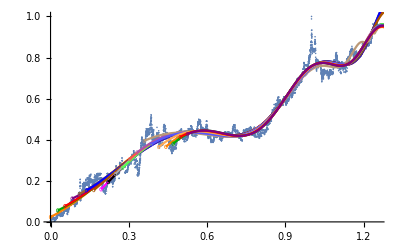

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0276243,0.0552486,0.0828729,0.110497,0.138122,0.165746,0.19337,0.220994,0.248619,0.276243,0.303867,0.331492,0.359116,0.38674,0.414365,0.441989,0.469613,0.497238,0.524862}

{0.00114531,0.00116154,0.00117548,0.00118519,0.00119431,0.00120743,0.00119165,0.00112497,0.00113652,0.00116012,0.00118088,0.0011978,0.00121459,0.00112053,0.00102727,0.000953397,0.000889288,0.000866389,0.000879034,0.000899738}

{9.94357,9.8615,9.75417,9.60836,9.45295,9.32497,8.9755,8.25726,8.12499,8.07098,7.98868,7.87436,7.75152,6.93719,6.1626,5.53638,4.99424,4.6993,4.59998,4.53558}

{0.0338307,0.0340694,0.0342729,0.0344139,0.0345457,0.0347346,0.0345065,0.0335268,0.0336982,0.0340459,0.0343488,0.0345935,0.0348346,0.0334581,0.0320351,0.0308612,0.029805,0.0294182,0.0296315,0.0299778}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

8689

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

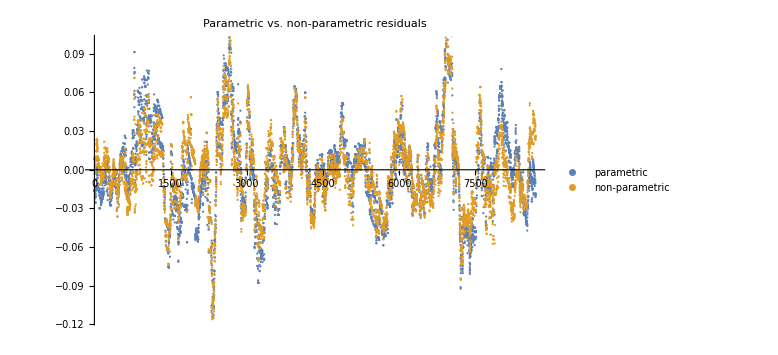

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{7.76477,9.94357}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0299294,0.0338424}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000895767,0.00114531}

```mathematica
selN=Length[T1s];
selN
```

20

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609,4369,4129}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609,4369,4129}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{8689,8449,8209,7969,7729,7489,7249,7009,6769,6529,6289,6049,5809,5569,5329,5089,4849,4609,4369,4129}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00114531,0.00116154,0.00117548,0.00118519,0.00119431,0.00120743,0.00119165,0.00112497,0.00113652,0.00116012,0.00118088,0.0011978,0.00121459,0.00112053,0.00102727,0.000953397,0.000889288,0.000866389,0.000879034,0.000899738}

```mathematica
RSSs
```

{9.94357,9.8615,9.75417,9.60836,9.45295,9.32497,8.9755,8.25726,8.12499,8.07098,7.98868,7.87436,7.75152,6.93719,6.1626,5.53638,4.99424,4.6993,4.59998,4.53558}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0298951,0.0302746,0.0306462,0.0309706,0.031236,0.0313611,0.0313872,0.0313792,0.0316237,0.0320515,0.0308582,0.0302685,0.0294613,0.0293712,0.0289788,0.0294145,0.0299514,0.029873,0.0300869,0.0307425}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.950716,σ→-0.00926881,μ→-6.64577×10^-6},{ρ→0.950734,σ→-0.00938477,μ→-0.0000128747},{ρ→0.951109,σ→-0.00946462,μ→-3.85898×10^-6},{ρ→0.951318,σ→-0.00954486,μ→9.76461×10^-6},{ρ→0.953192,σ→-0.00944406,μ→-4.89342×10^-7},{ρ→0.954602,σ→-0.00934134,μ→-0.0000303093},{ρ→0.954989,σ→-0.00931007,μ→-0.0000368854},{ρ→0.95551,σ→-0.00925492,μ→-5.25573×10^-7},{ρ→0.957421,σ→-0.0091289,μ→-0.0000187183},{ρ→0.957208,σ→-0.00927501,μ→-0.0000120005},{ρ→0.956168,σ→-0.00903514,μ→0.0000480859},{ρ→0.955796,σ→-0.0088991,μ→-0.0000156354},{ρ→0.956787,σ→-0.00856633,μ→-0.00006547},{ρ→0.957536,σ→-0.00846736,μ→-0.0000731784},{ρ→0.956082,σ→-0.00849286,μ→-0.0000148566},{ρ→0.957041,σ→-0.00852799,μ→-0.0000276373},{ρ→0.958903,σ→-0.00849731,μ→-0.0000358239},{ρ→0.957664,σ→-0.00859917,μ→-0.0000845302},{ρ→0.957216,σ→-0.00870543,μ→-0.0000722996},{ρ→0.95772,σ→-0.00884362,μ→-0.0000479328}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-6.64577×10^-6,{0.950716},0.0000859108],ARProcess[-0.0000128747,{0.950734},0.0000880739],ARProcess[-3.85898×10^-6,{0.951109},0.000089579],ARProcess[9.76461×10^-6,{0.951318},0.0000911043],ARProcess[-4.89342×10^-7,{0.953192},0.0000891903],ARProcess[-0.0000303093,{0.954602},0.0000872607],ARProcess[-0.0000368854,{0.954989},0.0000866773],ARProcess[-5.25573×10^-7,{0.95551},0.0000856536],ARProcess[-0.0000187183,{0.957421},0.0000833369],ARProcess[-0.0000120005,{0.957208},0.0000860259],ARProcess[0.0000480859,{0.956168},0.0000816338],ARProcess[-0.0000156354,{0.955796},0.000079194],ARProcess[-0.00006547,{0.956787},0.000073382],ARProcess[-0.0000731784,{0.957536},0.0000716961],ARProcess[-0.0000148566,{0.956082},0.0000721287],ARProcess[-0.0000276373,{0.957041},0.0000727266],ARProcess[-0.0000358239,{0.958903},0.0000722043],ARProcess[-0.0000845302,{0.957664},0.0000739456],ARProcess[-0.0000722996,{0.957216},0.0000757844],ARProcess[-0.0000479328,{0.95772},0.0000782096]}

{28347.7,27459.3,26611.1,25764.7,25071.7,24380.4,23627.1,22881.8,22188.,21297.2,20679.7,20004.3,19411.2,18677.3,17853.1,17028.4,16242.9,15385.5,14538.8,13668.5}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

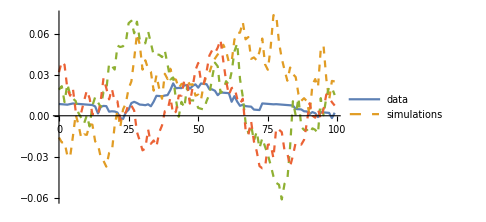
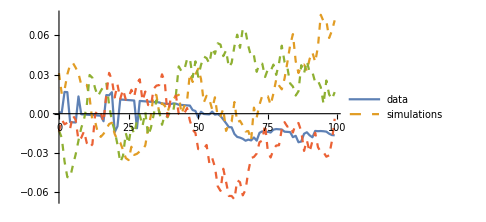
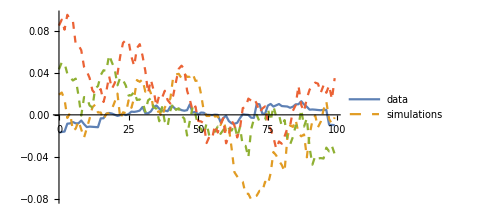
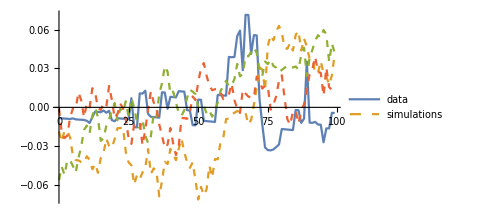
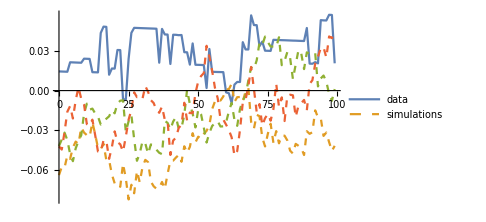
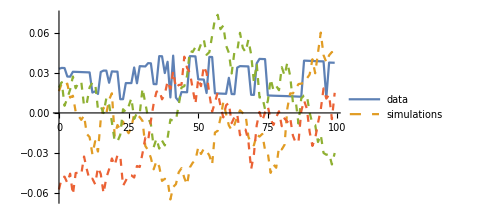
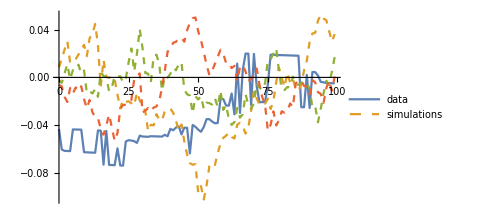
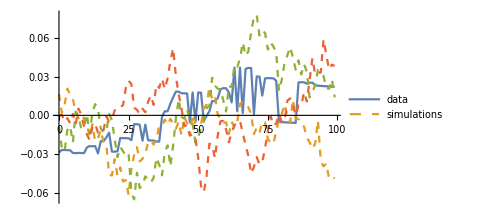

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{15.7132,8668.29},{15.7139,8428.29},{15.7145,8188.29},{15.7152,7948.29},{15.7158,7708.29},{15.7166,7468.29},{15.7173,7228.29},{15.7182,6988.28},{15.719,6748.28},{15.7201,6508.28},{15.721,6268.28},{15.7222,6028.28},{15.7233,5788.28},{15.7247,5548.28},{15.7261,5308.28},{15.7277,5068.27},{15.7293,4828.27},{15.7313,4588.27},{15.7333,4348.27},{15.7357,4108.27}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

8668.29

15.7132

{8668.29,8428.29,8188.29,7948.29,7708.29,7468.29,7228.29,6988.28,6748.28,6508.28,6268.28,6028.28,5788.28,5548.28,5308.28,5068.27,4828.27,4588.27,4348.27,4108.27}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 13.4336 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 13.4337 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2034828 Kb

Memory Used: 11.4933 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,4,2,4,50,59,67,2,0,0,3,10,148,536,633,644,676}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.004,0.002,0.004,0.05,0.059,0.067,0.002,0.,0.,0.003,0.01,0.148,0.536,0.633,0.644,0.676}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,False,False,False,True,True,True,True,True,False,False,False,False,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

8

```mathematica
(* As a fallback (if all rejected), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.2527

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

14

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,minTcIndex]
```

8

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.15682,b→-0.873274,c→0.113221,d→-0.0228418,T_1→0.19337,tc→1.40739,m→0.7,ω→7.,RSS→8.25726,ℛerror→0.00112497,ℛσ→0.0335268,LL→23948.9,ρ→0.960658,σ→-0.00931093,μ→-4.89477×10^-17,index→8}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

8

{a→1.15682,b→-0.873274,c→0.113221,d→-0.0228418,T_1→0.19337,tc→1.40739,m→0.7,ω→7.,RSS→8.25726,ℛerror→0.00112497,ℛσ→0.0335268,LL→23948.9,ρ→0.960658,σ→-0.00931093,μ→-4.89477×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.7

7.

1.40739

23948.9

```mathematica
t1=Subscript[T, 1]/.fit
```

0.19337

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

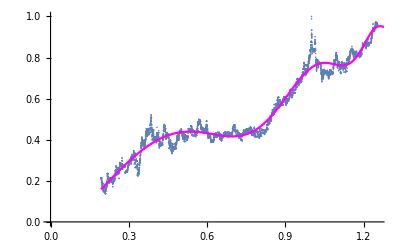

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.15682,b→-0.873274,c→0.113221,d→-0.0228418,T_1→0.19337,tc→1.40739,m→0.7,ω→7.,RSS→8.25726,ℛerror→0.00112497,ℛσ→0.0335268,LL→23948.9,ρ→0.960658,σ→-0.00931093,μ→-4.89477×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.960658,σ→-0.00931093,μ→-4.89477×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92005

{1.40198,1.40739}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92009

{1.40198,1.40739,1.41265}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.2526

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Tue 10 Feb 2026 04:09:53

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Wed 11 Feb 2026 17:39:57

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Fri 13 Feb 2026 06:09:47

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Mon 2 Mar 2026 04:16:01

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Wed 8 Apr 2026 14:52:53

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Mon 29 Dec 2025 00:41:36

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Wed 1 Jan 2025 00:00:00 | tc→1.48474 | Fri 6 Mar 2026 02:09:07
T_1→0.0276243 | Wed 8 Jan 2025 23:36:07 | tc→1.52341 | Tue 17 Mar 2026 06:23:42
T_1→0.0552486 | Thu 16 Jan 2025 23:12:15 | tc→1.52341 | Tue 17 Mar 2026 06:23:42
T_1→0.0828729 | Fri 24 Jan 2025 22:48:23 | tc→1.60076 | Wed 8 Apr 2026 14:52:53
T_1→0.110497 | Sat 1 Feb 2025 22:24:31 | tc→1.58142 | Fri 3 Apr 2026 00:45:35
T_1→0.138122 | Sun 9 Feb 2025 22:00:39 | tc→1.58142 | Fri 3 Apr 2026 00:45:35
T_1→0.165746 | Mon 17 Feb 2025 21:36:47 | tc→1.50408 | Wed 11 Mar 2026 16:16:25
T_1→0.19337 | Tue 25 Feb 2025 21:12:55 | tc→1.40739 | Wed 11 Feb 2026 17:39:57
T_1→0.220994 | Wed 5 Mar 2025 20:49:03 | tc→1.42673 | Tue 17 Feb 2026 07:47:15
T_1→0.248619 | Thu 13 Mar 2025 20:25:11 | tc→1.40739 | Wed 11 Feb 2026 17:39:57
T_1→0.276243 | Fri 21 Mar 2025 20:01:19 | tc→1.42673 | Tue 17 Feb 2026 07:47:15
T_1→0.303867 | Sat 29 Mar 2025 19:37:27 | tc→1.40739 | Wed 11 Feb 2026 17:39:57
T_1→0.331492 | Sun 6 Apr 2025 19:13:35 | tc→1.40739 | Wed 11 Feb 2026 17:39:57
T_1→0.359116 | Mon 14 Apr 2025 18:49:43 | tc→1.2527 | Mon 29 Dec 2025 00:41:36
T_1→0.38674 | Tue 22 Apr 2025 18:25:51 | tc→1.40739 | Wed 11 Feb 2026 17:39:57
T_1→0.414365 | Wed 30 Apr 2025 18:01:59 | tc→1.44607 | Sun 22 Feb 2026 21:54:32
T_1→0.441989 | Thu 8 May 2025 17:38:07 | tc→1.48474 | Fri 6 Mar 2026 02:09:07
T_1→0.469613 | Fri 16 May 2025 17:14:15 | tc→1.52341 | Tue 17 Mar 2026 06:23:42
T_1→0.497238 | Sat 24 May 2025 16:50:23 | tc→1.50408 | Wed 11 Mar 2026 16:16:25
T_1→0.524862 | Sun 1 Jun 2025 16:26:31 | tc→1.52341 | Tue 17 Mar 2026 06:23:42

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

1.15546

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

1.13485

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.9616

```mathematica
lastPriceDate
```

2025-12-29

```mathematica
(* Closing price at `lastPriceDate` date: *)
```

```mathematica
latestPrice=hourlyPrices[[-1]][[2]]
```

4375.59

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

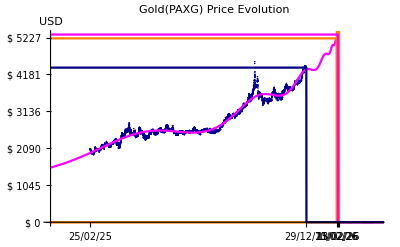

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Gold(PAXG) Price Evolution",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Gold(PAXG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/Gold(PAXG)_PricePrediction-2025-12-29.png

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

4375.59

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

5203.28

```mathematica
bestPrice=pToPrice[bestP]
```

5311.64